# Computational Science

## Machine Learning for Physicists Project: Unsupervised and supervised analysis of protein sequences

This notebook is 100% human-made and has been created without any LLM.

Paul Cousin

Université Paris Cité • 2025/2026

## Note to the reader

Cells colored in blue will be code cells.

Cells colored in pink will be text comments.

## Import and format data

```mathematica
formatData[s_String]:=Module[{string=s},
string//=StringSplit[#,">"]&;
string//=StringDelete[#,"\n"]&;
string//=StringReplace[#,"sequence_"~~x:NumberString~~" functional_"~~y:("true"|"false")~~z__~~WordBoundary:>x~~","~~y~~","~~z]&;string//=StringSplit[#,","]&;
string/.{x_,y_,z_}:>{ToExpression@x,y=="true",z}
];
```

formatData is a function that formats the content of the .faa files which is encapsulated in  and  in the following cell.

```mathematica
natSeq=formatData@;
artSeq=formatData@;
```

Here is an example of how a sequence is now formatted.

```mathematica
natSeq[[1]]
```

{1,True,-TSENPLLALREKISALDEKLLALLAERRELAVEVGKAKLLSHRPVRDIDRERDLLERLITLGK-AHHLDAHYITRLFQLIIEDSVLTQQALLQQH}

## Task 1: One-hot encoding of protein sequence data

```mathematica
characterMap={"A"->1,"C"->2,"D"->3,"E"->4,"F"->5,"G"->6,"H"->7,"I"->8,"K"->9,"L"->10,"M"->11,"N"->12,"P"->13,"Q"->14,"R"->15,"S"->16,"T"->17,"V"->18,"W"->19,"Y"->20};
```

```mathematica
vectorize[seq_]:=SparseArray[If[#!="-",#->1,{}],20]&/@Replace[characterMap]/@StringPartition[seq,1];
```

```mathematica
natSeqHot=SparseArray[vectorize/@natSeq[[;;,3]]];
artSeqHot=SparseArray[vectorize/@artSeq[[;;,3]]];
```

All the sequences have been one-hot encoded in the SparseArray format.

```mathematica
natSeqHot[[1]]
```

SparseArray[…]

```mathematica
ArrayPlot@Transpose@natSeqHot[[1]]
```

-Graphics-

## Task 2: Dimensional reduction and visualization of sequence space

The data is now stored in a 3-dimensional tensor. Its dimensions are:

```mathematica
Dimensions@natSeqHot
```

{1130,96,20}

We need to create a 1130×1130 covariance matrix from this data. We therefore need a way to combine two 96×20 matrices together and obtain a measure of their similitude. The simplest way is probably to count the number of elements the two matrices have in common by multiplying them term-by-term and computing the total. For example:

```mathematica
Total[natSeqHot[[1]]*natSeqHot[[2]],2]
```

23

The covariance matrix corresponds to the symmetric matrix where all sequences are compared to each other in this way.

```mathematica
covMatNat=Table[Total[natSeqHot[[i]]*natSeqHot[[j]],2],{i,1130},{j,1130}];
```

```mathematica
ArrayPlot[covMatNat,ColorFunction->"BlueGreenYellow",PlotLabel->"Covariance Matrix of the Natural Sequences"]
```

-Graphics-

Using the first eigenvalues and eigenvectors of this covariance matrix, we can project our data on the two or three most meaningful axes.

```mathematica
eigValNat=Eigenvalues[N@covarianceMatrix,3];
eigVecNat=Eigenvectors[N@covarianceMatrix,3];
```

```mathematica
projection[seq_]:=Total[Total[eigVecNat[[#]]*natSeqHot]*seq,2]&/@{1,2,3};
```

```mathematica
projectedNat=projection/@natSeqHot;
```

```mathematica
fontionalNatSeqIndices=Cases[natSeq,x_?(#[[2]]&):>x[[1]]];
nonFontionalNatSeqIndices=Complement[Range@Length@natSeq,fontionalNatSeqIndices];
```

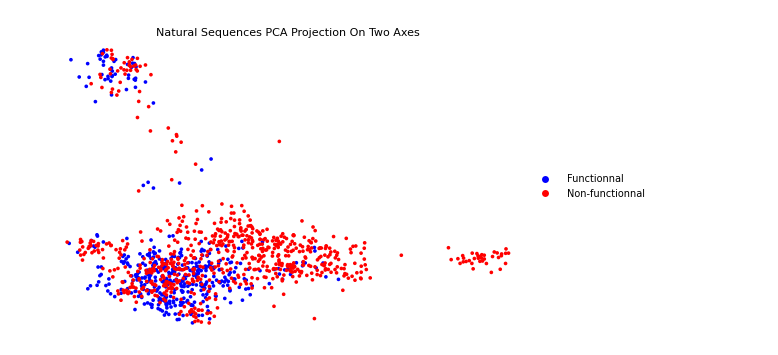

```mathematica
plotNat2D=ListPlot[{projectedNat[[fontionalNatSeqIndices,;;2]],projectedNat[[nonFontionalNatSeqIndices,;;2]]},
Axes->False,PlotRange->Full,ImageSize->Large,PlotLabel->"Natural Sequences\nPCA Projection On Two Axes",PlotStyle->{Blue,Red},PlotLegends-> {"Functionnal","Non-functionnal"},PlotRange->Full]
```

```mathematica
projectNat=(GroupBy[
Transpose[{
eigValNat[[1]]*Total[eigVecNat[[1]]*natSeqHot,{2,3}],
eigValNat[[2]]*Total[eigVecNat[[2]]*natSeqHot,{2,3}],
eigValNat[[3]]*Total[eigVecNat[[3]]*natSeqHot,{2,3}],
natSeq[[;;,2]]
}],#[[4]]&]/@{True,False})[[;;,;;,;;3]];
```

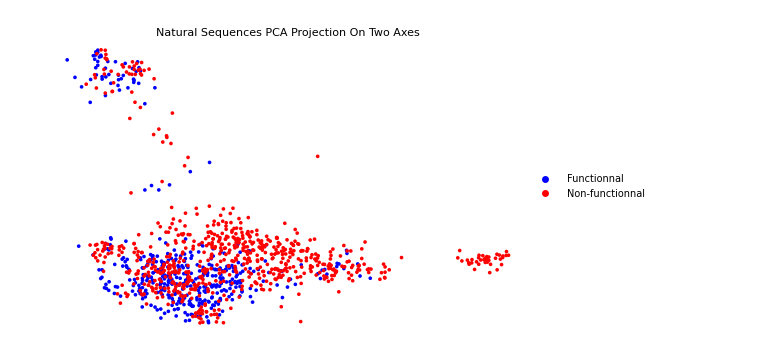

```mathematica
plotNat2D=ListPlot[projectNat[[;;,;;,;;2]],Axes->False,PlotRange->Full,ImageSize->Large,PlotLabel->"Natural Sequences\nPCA Projection On Two Axes",PlotStyle->{Blue,Red},PlotLegends-> {"Functionnal","Non-functionnal"},PlotRange->Full]
```

```mathematica
projection[seq_]:=Total[Total[eigVecNat[[#]]*natSeqHot]*seq,2]&/@{1,2,3};
```

```mathematica
projectedNat=(GroupBy[Table[Catenate@{projection@natSeqHot[[n]],{natSeq[[n,2]]}},
{n,Length@natSeqHot}],#[[4]]&]/@{True,False})[[;;,;;,;;3]];
```

```mathematica
plotNat2D=ListPlot[projectNat[[;;,;;,;;2]],Axes->False,PlotRange->Full,ImageSize->Large,PlotLabel->"Natural Sequences\nPCA Projection On Two Axes",PlotStyle->{Blue,Red},PlotLegends-> {"Functionnal","Non-functionnal"},PlotRange->Full]
```

-Graphics-

```mathematica
plotNat3D=ListPointPlot3D[projectNat,
Axes->False,PlotRange->Full,ImageSize->Large,PlotLabel->"Natural Sequences\nPCA Projection On Three Axes",PlotStyle->{Blue,Red},PlotLegends-> {"Functionnal","Non-functionnal"}]
```

-Graphics3D-

```mathematica
projectArt=(GroupBy[Table[{
Total[Total[eigValNat[[1]]*eigVecNat[[1]]*natSeqHot]*artSeqHot[[n]],2],
Total[Total[eigValNat[[2]]*eigVecNat[[2]]*natSeqHot]*artSeqHot[[n]],2],
Total[Total[eigValNat[[3]]*eigVecNat[[3]]*natSeqHot]*artSeqHot[[n]],2],
artSeq[[n,2]]},
{n,Length@artSeqHot}],#[[4]]&]/@{True,False})[[;;,;;,;;3]];
```

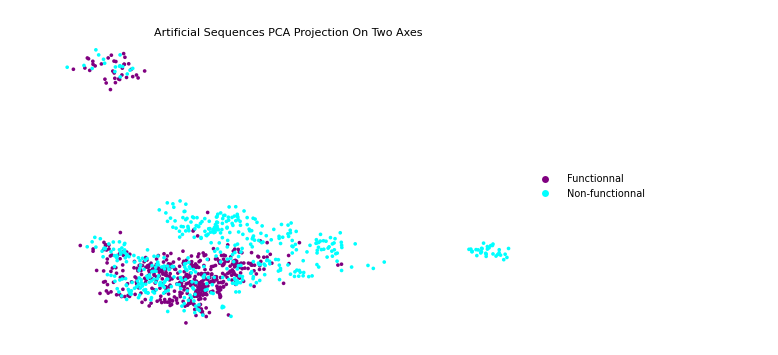

```mathematica
plotArt2D=ListPlot[projectArt[[;;,;;,;;2]],Axes->False,PlotRange->Full,ImageSize->Large,PlotLabel->"Artificial Sequences\nPCA Projection On Two Axes",PlotStyle->{Purple,Cyan},PlotLegends-> {"Functionnal","Non-functionnal"}]
```

```mathematica
plotArt3D=ListPointPlot3D[projectArt[[;;,;;,;;3]],
Axes->False,PlotRange->Full,ImageSize->Large,PlotLabel->"Natural Sequences\nPCA Projection On Three Axes",PlotStyle->{Purple,Orange},PlotLegends-> {"Functionnal","Non-functionnal"}]
```

-Graphics3D-

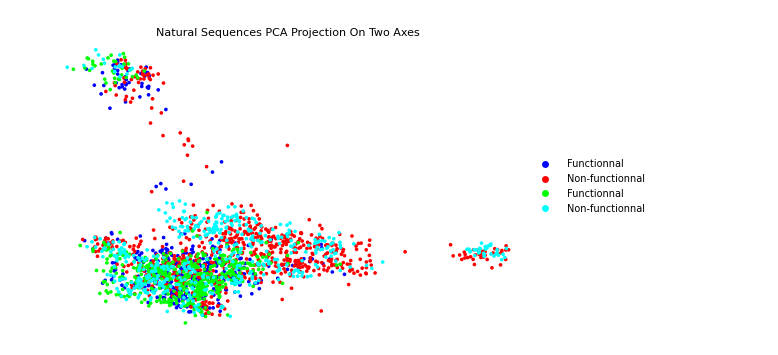

```mathematica
Show[{plotNat2D,plotArt2D},PlotRange->All]
```

```mathematica
(GroupBy[Table[{
Total[Total[eigValNat[[1]]*eigVecNat[[1]]*natSeqHot]*artSeqHot[[n]],2],
Total[Total[eigValNat[[2]]*eigVecNat[[2]]*natSeqHot]*artSeqHot[[n]],2],
Total[Total[eigValNat[[3]]*eigVecNat[[3]]*natSeqHot]*artSeqHot[[n]],2],
artSeq[[n,2]]},
{n,Length@artSeqHot}],#[[4]]&]/@{True,False})[[;;,;;,;;3]];
```

```mathematica
Dimensions[Total[Total[eigValNat[[1]]*eigVecNat[[1]]*natSeqHot]*#&/@artSeqHot,{2,3}]]
```

{1003}

```mathematica
Dimensions@Total[Total[eigValNat[[1]]*eigVecNat[[1]]*natSeqHot]*artSeqHot[[1]],2]
```

{}

```mathematica
test1=Table[{
Total[Total[eigValNat[[1]]*eigVecNat[[1]]*natSeqHot]*artSeqHot[[n]],2],
Total[Total[eigValNat[[2]]*eigVecNat[[2]]*natSeqHot]*artSeqHot[[n]],2],
Total[Total[eigValNat[[3]]*eigVecNat[[3]]*natSeqHot]*artSeqHot[[n]],2]
},{n,Length@artSeqHot}];
```

```mathematica
Table[{
Total[Total[eigValNat[[1]]*eigVecNat[[1]]*natSeqHot]*artSeqHot[[n]],2],
Total[Total[eigValNat[[2]]*eigVecNat[[2]]*natSeqHot]*artSeqHot[[n]],2],
Total[Total[eigValNat[[3]]*eigVecNat[[3]]*natSeqHot]*artSeqHot[[n]],2]
},{n,Length@artSeqHot}]
```

```mathematica
Total[Total[eigValNat[[1]]*eigVecNat[[1]]*natSeqHot]*artSeqHot[[1]],2]
```

-1.58064×10^7